```mathematica
g = 9.81;
radius = 1;
cRad = 0.05;
tmax = 1000;
reflected = ReflectionTransform[{-x[t], -y[t]}][{x'[t], y'[t]}];
frameRate = 144;
frameTime = 1 / frameRate;
color1 = RGBColor[1.0, 0.7, 0.29];
color2 = RGBColor[0.0, 0.86, 0.9];
colorBG = RGBColor[0.0, 0.07, 0.15];
```

```mathematica
solveSystem[x0_, y0_] := NDSolveValue [
{
y''[t]== -g,
x''[t]== 0,
x'[0]== 0,
y'[0]== 0,
x[0]== x0,
y[0]== y0,
WhenEvent[x[t]^2 + y[t]^2 == (radius-cRad) * (radius - cRad),
{x'[t], y'[t]}->Evaluate[reflected]
]
},
{x, y},
{t, 0, tmax}
];
```

```mathematica
{xf1, yf1} = solveSystem[0.001, 0.5];
{xf2, yf2} = solveSystem[0.00101, 0.5];
```

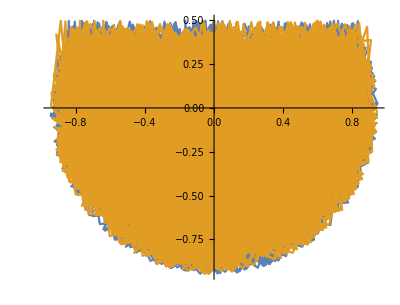

```mathematica
ParametricPlot[{{xf1[t], yf1[t]}, {xf2[t], yf2[t]}}, {t, 0, tmax}]
```

```mathematica
m = Table[Evaluate[If[j == 1, xf1[i], If[j == 2, yf1[i], If[j == 3, xf2[i], yf2[i]]]]], {i, 0, tmax, frameTime}, {j, 4}];
m // TableForm
Export["mfile.csv",m,"CSV"]
```

1
 |  |  |  |

mfile.csv

```mathematica
list=Table[Graphics[{
{colorBG, Rectangle[{-1.1, 1.1}, {1.1, -1.1}]},
{White, Thick,Circle[{0, 0}, 1]},
{Thick, color1, Line[Table[{xf1[j], yf1[j]}, {j, 0, i, frameTime}]]},
{Thick, color2, Line[Table[{xf2[j], yf2[j]}, {j, 0, i, frameTime}]]},
{color1,Disk[{xf1[i], yf1[i]}, cRad]},
{color2,Disk[{xf2[i], yf2[i]},cRad]}
}], {i, 0, tmax, frameTime}];
ListAnimate[list]
```

```mathematica
Export["output.avi",list, Antialiasing->True, FrameRate->frameRate, RasterSize-> 2160, CompressionLevel-> 0]
```

output.avi

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\bmalh\Desktop\Projects\Mathematica\Testing Animation